```mathematica
g[x_]:=Piecewise[{{1,-1<x<1}}]
```

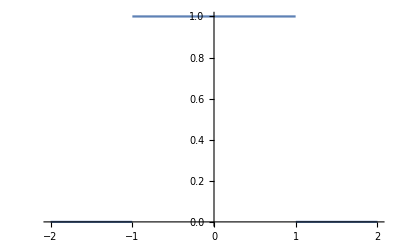

```mathematica
Plot[g[x],{x,-2,2}]
```

```mathematica
A[w_]:=1/π∫_(-∞)^∞ (g[x]*Cos[w*x])ⅆx
```

```mathematica
B[w_]:=1/π∫_(-∞)^∞ (g[x]*Sin[w*x])ⅆx
```

```mathematica
A[w]
```

(2 Sin[w])/(π w)

```mathematica
f[x]=∫_0^8 ((2*Sin[w])/(π*w)*Cos[w*x])ⅆw
```

(SinIntegral[8-8 x]+SinIntegral[8 (1+x)])/π

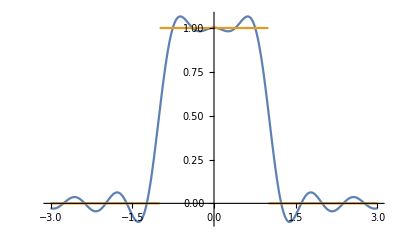

```mathematica
Plot[{f[x],g[x]},{x,-3,3}]
```

```mathematica
f[x]=∫_0^16 ((2*Sin[w])/(π*w)*Cos[w*x])ⅆw
```

(SinIntegral[16-16 x]+SinIntegral[16 (1+x)])/π

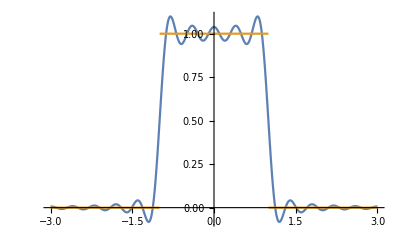

```mathematica
Plot[{f[x],g[x]},{x,-3,3}]
```

```mathematica
f[x]=∫_0^30 ((2*Sin[w])/(π*w)*Cos[w*x])ⅆw
```

(SinIntegral[30-30 x]+SinIntegral[30 (1+x)])/π

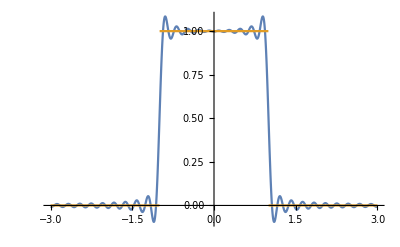

```mathematica
Plot[{f[x],g[x]},{x,-3,3}]
```

```mathematica
f[x]=∫_0^50 ((2*Sin[w])/(π*w)*Cos[w*x])ⅆw
```

(SinIntegral[50-50 x]+SinIntegral[50 (1+x)])/π

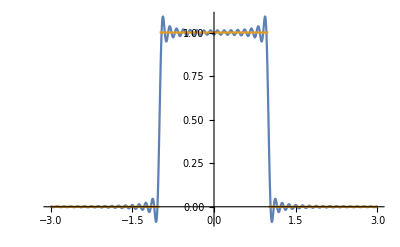

```mathematica
Plot[{f[x],g[x]},{x,-3,3}]
```

```mathematica
________________________________________________________________________________________________________________________
```

```mathematica
h[x_]:=Piecewise[{{x,-1<x<1}}]
```

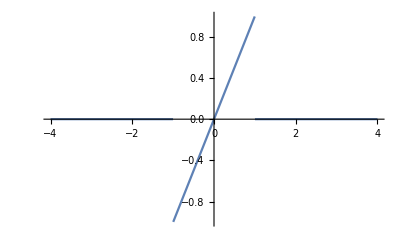

```mathematica
Plot[{h[x]},{x,-4,4}]
```

```mathematica
A[w_]:=1/π∫_-1^1 (h[x]*Cos[w*x])ⅆx
```

```mathematica
A[w]
```

(4 w Cos[w]+2 (-2+w^2) Sin[w])/(π w^3)

```mathematica
B[w_]:=1/π∫_-1^1 (g[x]*Sin[w*x])ⅆx
```

```mathematica
B[w]
```

0